```mathematica
A[x_,y_,z_]:={x z y,x y^2 z,z^2 x y^3};
Curl[A[x,y,z],{x,y,z}]
```

{-x y^2+3 x y^2 z^2,x y-y^3 z^2,-x z+y^2 z}

```mathematica
B[x_,y_,z_]:={-x y^2+3 x y^2 z^2,x y-y^3 z^2,-x z+y^2 z}
```

```mathematica
Div[B[x,y,z],{x,y,z}]
```

0

```mathematica
B[1,2,3]
```

{104,-70,9}

```mathematica
VectorPlot3D[B[x,y,z],{x,-1,1},{y,-1,1},{z,-2,2}]
```

-Graphics3D-

```mathematica
SliceVectorPlot3D[B[x,y,z], {"ZStackedPlanes",5},{x,-1,1},{y,-1,1},{z,-1,1}]
```

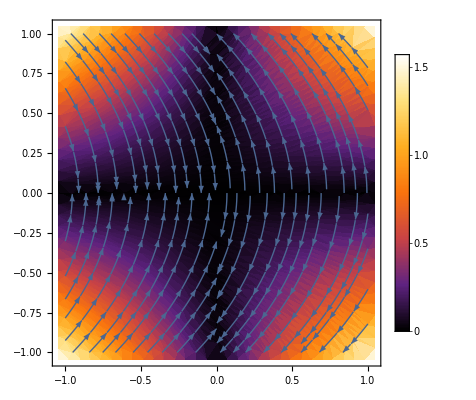

```mathematica
StreamDensityPlot[B[x,y,0][[1;;2]],{x,-1,1},{y,-1,1},ColorFunction->"SunsetColors",PlotLegends->Automatic]
```

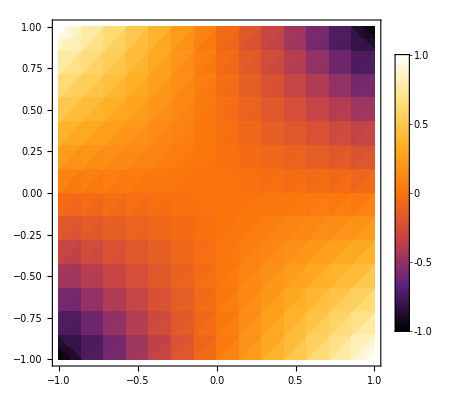

```mathematica
DensityPlot[B[x,-0.024999999999999967,z][[3]],{x,-1,1},{z,-1,1},ColorFunction->"SunsetColors",PlotLegends->Automatic]
```

```mathematica
B[-0.8,-0.825,-0.8][[3]]
```

```mathematica
-1.1845
```

-1.1845

```mathematica
B[-0.9714285714285714,-0.975,-0.8][[3]]
```

-1.53764

```mathematica
B[0.8571428571428571,0.8750000000000001,0.8666666666666667][[3]]
```

```mathematica
-0.07931547619047596+0.07931547619047474
```

-1.22125×10^-15

```mathematica
-1.9220535714285714+1.9220535714285698
```

-1.55431×10^-15

```mathematica
-0.9720535714285714+0.9720535714285714
```

0.

```mathematica
-0.8075595238095239+0.8075595238095238
```

-1.11022×10^-16

```mathematica
-0.8075595238095239
```

-0.80756

```mathematica
-1.2974464285714287+1.2974464285714302
```

1.55431×10^-15

```mathematica
-1.9012499999999999
```

-1.90125

```mathematica
-1.9012499999999999
```

-1.90125

```mathematica
-0.19339285714285714
```

-0.193393

```mathematica
-0.20854166666666665
```

-0.208542

```mathematica
A[-0.9714285714285714,-0.5,-1.0][[1]]
```

```mathematica
-0.4857142857142857
```

-0.485714

```mathematica
-0.9714285714285714
```

-0.971429